```mathematica
eq1=(r*b[r]*c[r]*a'[r]^2-2r*a[r]*b[r]*c[r]*a''[r]+r*a[r]*c[r]*a'[r]*b'[r]-2r*a[r]*b[r]*a'[r]*c'[r]-4a[r]b[r]c[r]a'[r])/(4*r*a[r]*b[r]^2*c[r])==a[r]*Λ;
eq2=1/(4r*a[r]^2 b[r] c[r]^2)(r*b[r]*c[r]^2*a'[r]^2-2r*a[r]b[r]*c[r]^2*a''[r]+2r*a[r]^2 b[r] c'[r]^2-4r*a[r]^2 b[r]c[r]c''[r]+b'[r](r*a[r] c[r]^2 a'[r]+4 a[r]^2 c[r]^2)+c'[r]*2(r*a[r]^2 c[r]b'[r]-4 a[r]^2 b[r]c[r]))==b[r]*Λ;
eq3=(2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r] b[r]^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r]))/(4*a[r] b[r]^2)==-c[r]*r^2*Λ;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

4 Λ a[r] b[r]+a'[r] (4/r-b'[r]/b[r]+(2 c'[r])/c[r])+2 a''[r]==a'[r]^2/a[r]

c[r] (-(a'[r] b'[r])/b[r]+2 a''[r])+a[r] (4 Λ b[r] c[r]+(8 c'[r])/r-(2 c'[r]^2)/c[r]-(2 b'[r] (2 c[r]+r c'[r]))/(r b[r])+4 c''[r])==(c[r] a'[r]^2)/a[r]

4 c[r]+4 b[r] (-1+r^2 Λ c[r])+(r a'[r] (2 c[r]+r c'[r]))/a[r]+2 r (4 c'[r]+r c''[r])==(r b'[r] (2 c[r]+r c'[r]))/b[r]

## Working the special case c(r) = 1

```mathematica
c[r_]:=1
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

4 Λ a[r] b[r]+a'[r] (4/r-b'[r]/b[r])+2 a''[r]==a'[r]^2/a[r]

4 Λ a[r] b[r]+2 a''[r]==a'[r]^2/a[r]+((4 a[r]+r a'[r]) b'[r])/(r b[r])

2+2 (-1+r^2 Λ) b[r]+(r a'[r])/a[r]==(r b'[r])/b[r]

### Method 1

```mathematica
FullSimplify[Solve[eq1,a''[r]]]
FullSimplify[Solve[eq2,a''[r]]]
```

{{a''[r]→1/2 (-4 Λ a[r] b[r]+a'[r]^2/a[r]+a'[r] (-4/r+b'[r]/b[r]))}}

{{a''[r]→1/2 (a'[r]^2/a[r]+(a'[r] b'[r])/b[r]+a[r] (-4 Λ b[r]+(4 b'[r])/(r b[r])))}}

```mathematica
FullSimplify[1/2 (-4 Λ a[r] b[r]+a'[r]^2/a[r]+a'[r] (-4/r+b'[r]/b[r]))==1/2 (a'[r]^2/a[r]+(a'[r] b'[r])/b[r]+a[r] (-4 Λ b[r]+(4 b'[r])/(r b[r])))]
```

(b[r] a'[r]+a[r] b'[r])/(r b[r])==0

```mathematica
b[r_]:=Subscript[c, 0]/a[r];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

(a[r] (2 r Λ c_0+2 a'[r]+r a''[r]))/(r c_0)==0

(2 r Λ c_0+2 a'[r]+r a''[r])/(r a[r])==0

(a[r]+(-1+r^2 Λ) c_0+r a'[r])/c_0==0

```mathematica
DSolve[eq1,a[r],r]
```

{{a[r]→0},{a[r]→-C[1]/r+C[2]-1/3 r^2 Λ c_0}}

```mathematica
Print["This is a(r) function"]
a[r_]:=-C[1]/r+C[2]-1/3 r^2 Λ Subscript[c, 0]
Print["This is b(r) function"]
FullSimplify[b[r]]
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

This is a(r) function

This is b(r) function

-(3 r c_0)/(3 C[1]-3 r C[2]+r^3 Λ c_0)

True

True

C[2]/c_0==1

```mathematica
a[r_]:=-C[1]/r+C[0]-1/3 r^2 Λ Subscript[c, 0];
b[r_]:=-(3 r Subscript[c, 0])/(3 C[1]-3 r C[0]+r^3 Λ Subscript[c, 0]);
c[r_]:=1;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

C[0]/c_0==1

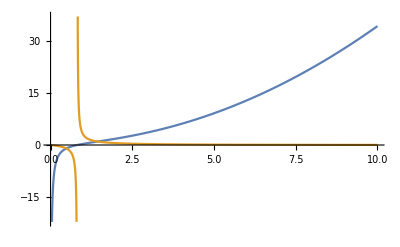

```mathematica
Plot[{-1/r+1-1/3 r^2 (-1) 1,-(3 r)/(3 -3 r +r^3 (-1))},{r,0,10}]
```

### Method 2

```mathematica
FullSimplify[Solve[eq2,b'[r]]]
```

{{b'[r]→(r b[r] (-a'[r]^2+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]))}}

```mathematica
b'[r]=(r b[r] (-a'[r]^2+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]));
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

(a[r] (2 r Λ a[r] b[r]+2 a'[r]+r a''[r]))/(r b[r] (4 a[r]+r a'[r]))==0

True

(-2 a[r]^2 (-2+(2+r^2 Λ) b[r])+r^2 a'[r]^2-r a[r] ((-3+b[r]) a'[r]+r a''[r]))/(a[r] b[r] (4 a[r]+r a'[r]))==-r^2 Λ

```mathematica
FullSimplify[Solve[eq1,b[r]]]
```

{{b[r]→-(2 a'[r]+r a''[r])/(2 r Λ a[r])}}

```mathematica
b[r]=-(2 a'[r]+r a''[r])/(2 r Λ a[r]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

r^2 Λ==1+(2 r Λ (a[r]+r a'[r]))/(2 a'[r]+r a''[r])

```mathematica
DSolve[eq3,a[r],r]
```

{{a[r]→C[1]/r+1/3 (3-r^2 Λ) C[2]}}

```mathematica
a[r_]:=C[1]/r+1/3 (3-r^2 Λ) C[2];
b[r_]:=(3 r C[2])/(3 C[1]+r (3-r^2 Λ) C[2]);
c[r_]:=1;
```

```mathematica
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

## Arbitrary case, make sense?